```mathematica
LineModelPlot[data_,xLabel_String,yLabel_String,Xmin_,Xmax_,title_String]:=
Module[{line},
line=Fit[data,{1,x},x];
Show[Plot[line,{x,Xmin,Xmax},PlotLabels->StringJoin[ToString[line],"\n\n","R^2=",ToString[(Correlation@@Transpose[data])^2]],PlotLabel->title,AxesLabel->{xLabel,yLabel},PlotStyle->Black,LabelStyle->{Black,12}],ListPlot[data,PlotStyle->Black],ImageSize->Large]
];
```

```mathematica
a={#1/10/0.05,#2}&@@@{{0.00,0.000},{0.20,0.092},{0.40,0.171},{0.80,0.353},{1.20,0.508},{1.60,0.661},{2.00,0.823}};
b={#1/10/0.05,#2}&@@@{{0.00,0.075},{0.20,0.158},{0.40,0.236},{0.80,0.393},{1.20,0.576},{1.60,0.717},{2.00,0.873}};
list1={440,450,460,470,480,490,500,506,508,510,520,530,540};
list2={0.128,0.138,0.150,0.161,0.171,0.174,0.180,0.184,0.185,0.186,0.178,0.143,0.098};
list3={0.369,0.398,0.427,0.458,0.482,0.491,0.507,0.520,0.524,0.525,0.501,0.408,0.285};
list4={0.528,0.624,0.669,0.715,0.756,0.770,0.796,0.818,0.823,0.825,0.787,0.640,0.443};
list=Transpose[{list1,#}]&/@{list2,list3,list4};
list5=Transpose[{{1.02,1.38,4.42,5.65,8.36,11.38,12.35,12.71},{0.158,0.315,0.398,0.403,0.407,0.394,0.379,0.305}}];
list6=Transpose[{{0.30,0.50,1.00,1.50,2.00,3.00,4.00},{0.156,0.300,0.413,0.414,0.405,0.415,0.412}}];
list7=Transpose[{{0.00,0.10,0.15,0.20,0.30,0.40,0.50,0.60,0.80,1.00},{0.000,0.236,0.344,0.455,0.507,0.437,0.356,0.282,0.127,0.004}}];
list8=Transpose[{{0,5,10,15,30,60,120},{0.400,0.398,0.398,0.401,0.392,0.385,0.422}}];
```

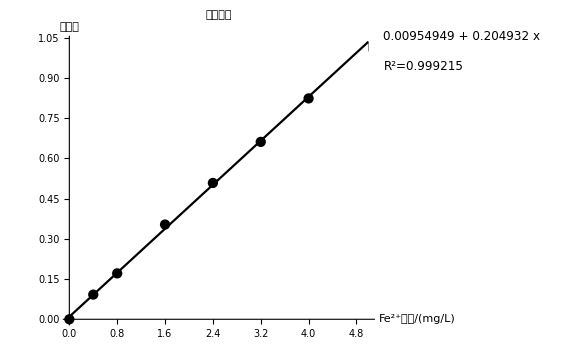

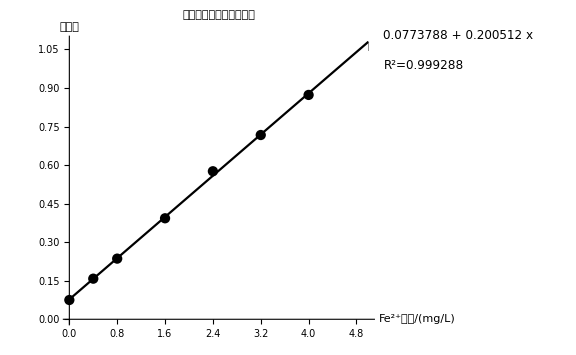

```mathematica
Quiet[LineModelPlot[a,"Fe^(2+)浓度/(mg/L)","吸光度",0,5,"标准曲线"]]

Quiet[LineModelPlot[b,"Fe^(2+)浓度/(mg/L)","吸光度",0,5,"空气为参比时的标准曲线"]]
```

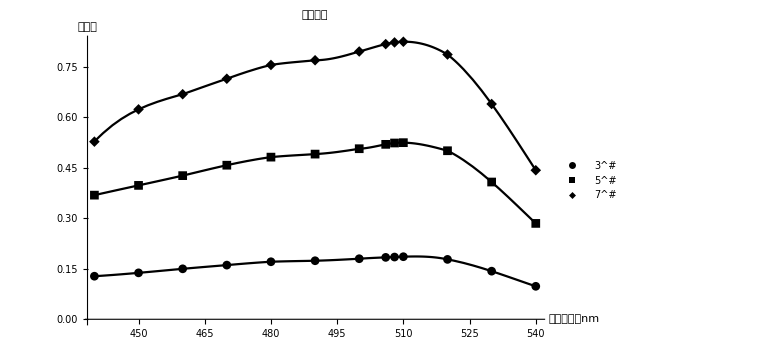

```mathematica
Show[ListPlot[list,PlotStyle->Black,PlotMarkers->Automatic,PlotLegends->{"3^#","5^#","7^#"},AxesLabel->{"测定波长／nm","吸光度"},PlotLabel->Style["吸收曲线",Black],LabelStyle->{Black,12}],Plot[(Interpolation[#,Method->"Hermite"][x]&/@list),{x,440,540},PlotStyle->Black],ImageSize->Large]
```

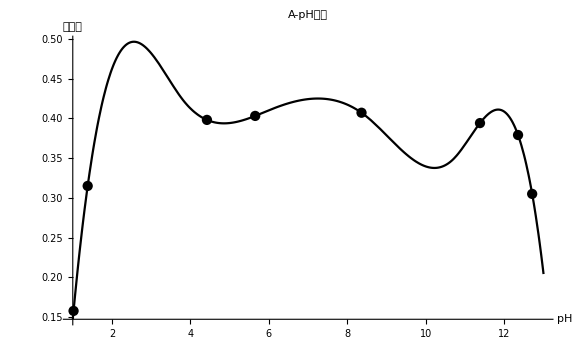

```mathematica
Show[Plot[Interpolation[list5,Method->"Spline"][x],{x,1,13},PlotStyle->Black,PlotRange->All,AxesLabel->{"pH","吸光度"},PlotLabel->Style["A-pH曲线",Black],LabelStyle->{Black,12}],ListPlot[list5,PlotStyle->Black],ImageSize->Large]
```

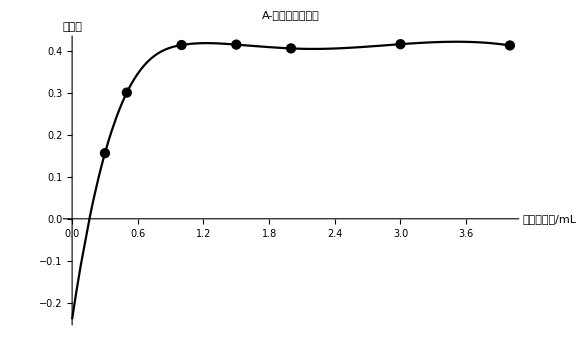

```mathematica
Show[Plot[Interpolation[list6,Method->"Spline"][x],{x,0,4},PlotStyle->Black,PlotRange->All,AxesLabel->{"显色剂用量/mL","吸光度"},PlotLabel->Style["A-显色剂用量曲线",Black],LabelStyle->{Black,12}],ListPlot[list6,PlotStyle->Black],ImageSize->Large]
```

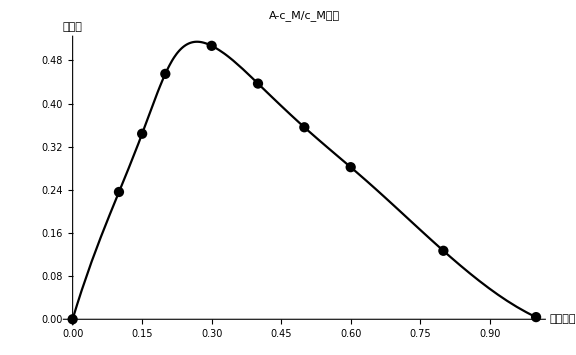

```mathematica
Show[Plot[Interpolation[list7,Method->"Spline"][x],{x,0,1},PlotStyle->Black,PlotRange->All,AxesLabel->{"摩尔分数","吸光度"},PlotLabel->Style["A-c_M/c_M曲线",Black],LabelStyle->{Black,12}],ListPlot[list7,PlotStyle->Black],ImageSize->Large]
```

```mathematica
Solve[D[Interpolation[list7,Method->"Spline"][x],x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.268365}}

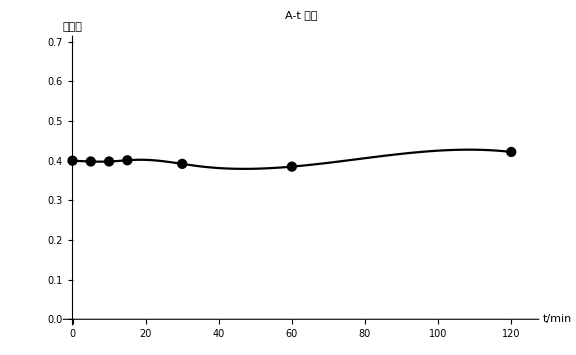

```mathematica
Show[Plot[Interpolation[list8,Method->"Spline"][x],{x,0,120},PlotStyle->Black,PlotRange->{{0,125},{0,0.7}},AxesLabel->{"t/min","吸光度"},PlotLabel->Style["A-t 曲线",Black],LabelStyle->{Black,12}],ListPlot[list8,PlotStyle->Black],ImageSize->Large]
```

```mathematica
CorrelationTest[a,b,{"TestDataTable",All}]
```

| Statistic | P-Value
Pearson Correlation | 0.999608 | 0.945626
Spearman Rank | 1. | 0.

```mathematica
IndependenceTest[a,b,{"TestDataTable",All}]
```

| Statistic | P-Value
Blomqvist β | 6.73024 | 0.150849
Kendall τ | 11.0331 | 0.0261951
Pillai Trace | 1.07216 | 0.111485
Spearman Rank | 7.00138 | 0.135815
Wilks 𝒲 | 1. | 0.

```mathematica
Solve[Fit[a,{1,x},x]==0.553,x]
```

{{x→0.0265186}}

```mathematica
Mean@Select[((#1-#3)(#2-#3)^3)/#3&@@@(Flatten[{#1*5*2*10^-3/50,(5-#1*5)2*10^-3/50,(x/.Solve[Fit[a,{1,x},x]==#2,x])/56/1000}]&@@@list7),Positive]
```

3.8556×10^-13